```mathematica
SetDirectory[NotebookDirectory[]];
Import["FunctionsAndConstants.wl"] ;(* parents directory could be "../LLR/FunctionsAndConstants.wl" etc*)
Needs["NDSolve`FEM`"];
Needs["NumericalCalculus`"];
Needs["MaTeX`"]
Clear[rhoV,rhoM,ρV,ρM]

ρV= SetPrecision[1.6726*10^-20*kgm32MeV4,1000]; (*roughly density of interplanatery medium*)
rhoE=SetPrecision[0.0000236851,5 CPrec]; (*mean density of the earth in MeV^4 *)
rhoS=SetPrecision[1408*kgm32MeV4,5 CPrec]; (* mean density of the sun in MeV^4 *)
rhoM=SetPrecision[0.0000143877,5 CPrec]; (*mean density of the moon in MeV^4, Pitschmannvalue*)
rhoN=SetPrecision[1.435550104*10^10,5 CPrec]; (*neutron density in MeV^4, Pitschmannvalue*)

RE=SetPrecision[6378100*m2invMeV,5 CPrec]; (*equatorial radius of the earth in MeV*)
RS=SetPrecision[695700000*m2invMeV,5 CPrec]; (*equatorial radius of the sun in MeV*)
RM=SetPrecision[1738100*m2invMeV,5 CPrec]; (*equatorial radius of the moon in MeV*)
RN=SetPrecision[0.0025,5 CPrec]; (*Neutron radius MeV^-1 - Pitschmann value*)

ME=SetPrecision[5.9724*10^(24)*kg2MeV,5 CPrec]; (*total mass of the earth in MeV*)
MS=SetPrecision[1.9891*10^(30)*kg2MeV,5 CPrec]; (*total mass of the sun in MeV*)
MN=SetPrecision[939.565346,5 CPrec]; (* neutron mass in MeV, Pitschmann value *)

ρE = rhoE;
ρS = rhoS;
ρM = rhoM;
ρN = rhoN;

aG=SetPrecision[1.30199*10^(-32),5 CPrec]; (*acceleration of earth towards sun in MeV, Pitschmann value*)

RES=SetPrecision[149597870700*m2invMeV,5 CPrec]; (*Earth-Sun distance also known as AE or AU, Subscript[r, AU] in the paper*)
(*Define mirror density*)

REM=SetPrecision[385000558.4*m2invMeV,5 CPrec]; (*Earth-Moon distance in MeV^-1*) 
GN=SetPrecision[6.70861*^-45,5 CPrec]; (*newtons constant in MeV^(-2), Pitschmann value*)


Q[A_,λ_,β_,ρ_,ρV_,R_]:=If[μ[A,λ,β,ρ] R<100,3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R) Tanh[SetPrecision[μ[A,λ,β,ρ] R,1000]])/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ] Tanh[μ[A,λ,β,ρ] R]),3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R))/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ])]

ϕ[r_,R_,λ_,A2_,β_,ρs_]:=If[r<=R,SetPrecision[ϕρ[A2,λ,β,ρs]+(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρs])/Cosh[μ[A2,λ,β,ρs]R] (1+μ[A2,λ,β,ρV]R)/(μ[A2,λ,β,ρs]+μ[A2,λ,β,ρV]Tanh[μ[A2,λ,β,ρs]R]) Sinh[μ[A2,λ,β,ρs]r]/r,5 CPrec],SetPrecision[ϕρ[A2,λ,β,ρV]-Q[A2,λ,β,ρs,ρV,R] (μ[A2,λ,β,ρs]^2 R^3)/3 (ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρs]) E^(-μ[A2,λ,β,ρV](r-R))/r,5CPrec]]
```

## Mesh and density parameters for sphere

446

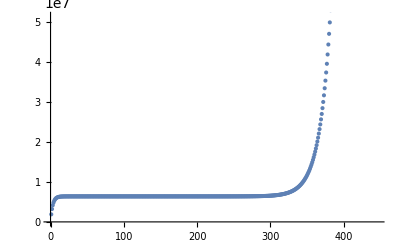

```mathematica
(*All manual definitions have to be made here*)

Clear[dd,nMaxRes,npts1,npts2,cutoff]
Clear[ SOLUTION,Vectorform,λ,A2,β,Prec,MAX,CPrec]
CPrec=500; (*you should not change this value*)

npts1=50;(*inside sphere, 400*)
npts2=300;(*outside sphere, 500*)
nFinePoints=50;(*this amount of points is placed next to the surfaces with minimum resolution*)
FAKTOR=SetPrecision[1,1000]; (*instead of using minmeshsize for nfine point you can use FAKTOR*Minmeshsize*)
cutoff=SetPrecision[(10*REM)/m2invMeV,1000]; (*Cutoff for boundary condition inside mirror in meters*)


minMeshSize=SetPrecision[cutoff*10^-10,5 CPrec];

Clear[R]
R=SetPrecision[RE/m2invMeV,1000]; (*Set Radius for sphere in meters*)

minMeshSize2=SetPrecision[R*10^-8,5 CPrec]; (*inside sphere!*)

Clear[R]
R=SetPrecision[RE/m2invMeV,1000]; (*Set Radius for sphere in meters*)

(*END OF MANUAL DEFINITIONS*)

coordlist[dmin_,ddelta_,dfactor_,nmin_,nmax_]:=Block[{i,dummy},
dummy=Table[N[dmin,5 CPrec],nmax-nmin+1];
If[nmin==0,
For[i=1,i<=nmax,i++,
dummy[[i+1]]=dummy[[i]]+N[ddelta*dfactor^i,5 CPrec];
];,
dummy[[1]]+=Sum[N[ddelta*dfactor^i,5 CPrec],{i,1,nmin}];
For[i=2,i<=nmax-nmin+1,i++,
dummy[[i]]=dummy[[i-1]]+N[ddelta*dfactor^(nmin+i-1),5 CPrec];
];];
N[dummy,5 CPrec]
];

Clear[rho,ρ];

rho[z_]:=SetPrecision[Piecewise[{{ρV,(R<z)},{ρE,z≤R}}],5CPrec];
ρ[z_]:=rho[z]

dist1=SetPrecision[cutoff,5CPrec];(* from -∞ to the border of the lower plate*)


f1=(*inside material*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize2,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts1-1}],5 CPrec]==SetPrecision[R-N[nFinePoints*minMeshSize2*FAKTOR,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];

f2=(*outside sphere*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts2-1}],5 CPrec]==SetPrecision[cutoff-R-N[nFinePoints*minMeshSize*FAKTOR,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];

points=SetPrecision[Sort[N[Join[

coordlist[N[-nFinePoints*minMeshSize2*FAKTOR+R,5 CPrec],-minMeshSize2,f1,1,npts1-1],
Table[N[-i*minMeshSize2*FAKTOR+R,5 CPrec],{i,0,nFinePoints-1}],
Table[N[i*minMeshSize*FAKTOR+R,5 CPrec],{i,1,nFinePoints}],
{R},

coordlist[N[nFinePoints*minMeshSize*FAKTOR+R,5 CPrec],minMeshSize,f2,1,npts2-2]]]](*free space from right*),5CPrec];

points[[-1]]=SetPrecision[cutoff,1000];
points=DeleteCases[points,0];
points=DeleteDuplicates[points];
Length[points]

ListPlot[points]
```

## Algorithm for units meters for distance - has to be activated!

```mathematica
Clear[b,A]
B[a_,b_,c_,rho_,ϕOld_,H_,points_,DVeff_,DDVeff_]:= Block[{Output},
Output={};

AppendTo[Output,DVeff[ϕOld[[1]],a,b,c,rho[[1]]]  -DDVeff[ϕOld[[1]],a,b,c,rho[[1]]]*ϕOld[[1]] ](*From first boundary condition*);
For[i=2, i<=Length[ϕOld]-1,i++, AppendTo[Output, DVeff[ϕOld[[i]],a,b,c,rho[[i]]]  -DDVeff[ϕOld[[i]],a,b,c,rho[[i]]]*ϕOld[[i]]]];
AppendTo[Output,DVeff[ϕOld[[-1]],a,b,c,rho[[-1]]]  -DDVeff[ϕOld[[-1]],a,b,c,rho[[-1]]]*ϕOld[[-1]] -Block[{$MaxExtraPrecision=1000},ϕρ[a,b,c,ρV]]/(H[[-1]]^2*m2invMeV^2)-Block[{$MaxExtraPrecision=1000},ϕρ[a,b,c,ρV]]/(H[[-1]]*points[[-1]]*m2invMeV^2)](*from 2nd bountady condition*);
(*I actually negelected a boundary term coming from the 2/r dphi/dr term, but this is highly suppressed for large r and vanishing gradient as is true at the boundary*);
Output]
(*Subscript[ρ, i] computes Subscript[ρ, i] prior to the iterations, such that it is not done repeadedly, same for Subscript[h, i]*)
ρi[points_]:=Block[{Output},
Output={};
For[i=1, i<=Length[points],i++, AppendTo[Output,ρ[points[[i]]]]];
Output]

h[points_]:=Block[{Output},
Output={};
For[i=1, i<=Length[points]-1,i++, AppendTo[Output,(points[[i+1]]-points[[i]])]];
AppendTo[Output,Output[[-1]]]; (*Subscript[h, N] would point outside the degrees of freedom and is therefore not part of points, I just repeat the last entry*);
Output]

(*H refers to the externally computed h, rho to Subscript[ρ, i]*)
(*B1 is the matrix for the second derivative*)

B1[a_,b_,c_,H_,rho_,ϕOld_,points_,DDVeff_]:=Block[{Output,h0},
h0=2*points[[1]]; (*this comes from the imaginary phi0 value at -points[[1]]*);
Output=ConstantArray[0,{Length[rho],Length[rho]}](*tridiagonal matrix with mostly 0 elements*); 
Output[[1]][[1]]=-(6/(H[[1]]*(H[[1]]+h0)*m2invMeV^2))-DDVeff[ϕOld[[1]],a,b,c,rho[[1]]] (*from boundary*);
Output[[1]][[2]]=(6/(H[[1]]*(H[[1]]+h0)*m2invMeV^2));

For[i=2, i<=Length[H]-1,i++, 
Output[[i]][[i+1]]=2/(H[[i]](H[[i]]+H[[i-1]])*m2invMeV^2)+2/points[[i]]*H[[i-1]]/(H[[i]](H[[i]]+H[[i-1]])*m2invMeV^2);
Output[[i]][[i-1]]=2/(H[[i-1]](H[[i]]+H[[i-1]])*m2invMeV^2)-2/points[[i]]*H[[i]]/(H[[i-1]](H[[i]]+H[[i-1]])*m2invMeV^2);
Output[[i]][[i]]= -(2/(H[[i]](H[[i]]+H[[i-1]])*m2invMeV^2))-2/(H[[i-1]](H[[i]]+H[[i-1]])*m2invMeV^2)+2/points[[i]]*(H[[i]]/(H[[i-1]](H[[i]]+H[[i-1]])*m2invMeV^2) -H[[i-1]]/(H[[i]](H[[i]]+H[[i-1]])*m2invMeV^2))-DDVeff[ϕOld[[i]],a,b,c,rho[[i]]](*from boundary*)];


Output[[-1]][[-2]]=1/((H[[-1]]^2)*m2invMeV^2)-1/((H[[-1]]*points[[-1]])*m2invMeV^2);
Output[[-1]][[-1]]=-(2/(H[[-1]]^2*m2invMeV^2))-DDVeff[ϕOld[[-1]],a,b,c,rho[[-1]]](*from boundary*);
Output

];

(*This function converts the continous function f into a discrete version that can be used as seed for newtons method*)
CreateSeed[f_,points_]:=Block[{Seed},
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,f[points[[i]]]]];
Seed]

(*The iterate function takes ϕ^(n-1) and returns ϕ^n*)

Clear[NORM]
NORM[Y1_]:=Sqrt[Sum[Y1[[i]]^2,{i,Length[points]}]]

Iterate[a_,b_,c_,H_,rho_,ϕOld_,DVeff_,DDVeff_,points_]:=Block[{Output,B3,C2},
B3=B[a,b,c,rho,ϕOld,H,points,DVeff,DDVeff];

C2=B1[a,b,c,H,rho,ϕOld,points,DDVeff];
Output=LinearSolve[C2,B3];
Output]

(*careful, Seed needs to be converted to a vector prior to using SOLVE*)
SOLVEFD[a_,b_,c_,points_,Prec_,Max_,Seed_,DVeff_,DDVeff_]:=Block[{YOLD,YNEW,DIFF,M,H,RHO,Func,Output},
M=2;
H=h[points];
RHO=ρi[points];
YOLD=If[StringQ[Seed],If[Seed=="Default",TrivialSeed2[points,a,b,c],Seed],Seed];
YNEW=Iterate[a,b,c,H,RHO,YOLD,DVeff,DDVeff,points];
DIFF=YNEW-YOLD;
While[(NORM[DIFF]/NORM[YOLD]>10^-Prec&&M<=Max),
M=M+1;
YOLD=YNEW;
YNEW=Iterate[a,b,c,H,RHO,YOLD,DVeff,DDVeff,points];
DIFF=YNEW-YOLD;
];
Func={};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],YNEW[[i]]}]];
Output=Interpolation[Func,InterpolationOrder->3];
M=M-1;
(*Print["iterations"M]*);
{YNEW,Output}]

TrivialSeed2[points_,a_,b_,c_]:=Block[{Seed,RHO},
RHO=ρi[points];
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,Block[{$MaxExtraPrecision=1000},ϕρ[a,b,c,RHO[[i]]]]]];
Seed]
```

## Compute Field

```mathematica
(*General Dilaton definitions*)
Clear[ϕρ,Veff,DVeff,DDVeff]
ϕρ[A_,λ_,β_,ρ_]:=SetPrecision[mpl/λ If[2*Log10[λ]+β-Log10[A]-Log10[ρ]<1000000,ProductLog[(λ^2 10^β)/(A ρ)],Log[λ^2/(A ρ)]+1/(6 (β Log[10]+Log[λ^2/(A ρ)])^3) (6 β Log[10] (β Log[10]+Log[λ^2/(A ρ)])^3-6 (-1+β Log[10]+Log[λ^2/(A ρ)]) (1+β^2 Log[10]^2+2 β Log[10] Log[λ^2/(A ρ)]+Log[λ^2/(A ρ)]^2) Log[β Log[10]+Log[λ^2/(A ρ)]]+3 (-3+β Log[10]+Log[λ^2/(A ρ)]) Log[β Log[10]+Log[λ^2/(A ρ)]]^2+2 Log[β Log[10]+Log[λ^2/(A ρ)]]^3)],1000]

μ[A_,λ_,β_,ρ_] :=SetPrecision[ Sqrt[SetPrecision[λ^2  E^SetPrecision[-λ ϕρ[A,λ,β,ρ]/mpl+β/Log10[E],1000] + A ρ,1000]]/mpl,1000]

Veff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/(2 mpl^2) ϕ^2,1000]

DVeff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[-λ/mpl*ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/mpl^2 ϕ,1000]
DDVeff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[λ^2/mpl^2*ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/mpl^2 ,1000]

Q[A_,λ_,β_,ρ_,ρV_,R_]:=If[μ[A,λ,β,ρ] R<100,3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R) Tanh[SetPrecision[μ[A,λ,β,ρ] R,1000]])/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ] Tanh[μ[A,λ,β,ρ] R]),3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R))/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ])]
```

{1.64063,Null}

InterpolatingFunction::dmval: Input value {78650.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

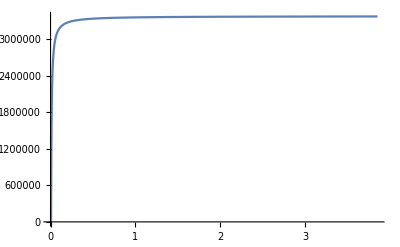

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=30;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(-24),1000];
A2=10^20;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

Plot[SOLUTION[z],{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {3146.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 7.2973×10^121 «1042» is too small to represent as a normalized machine number; precision may be lost.

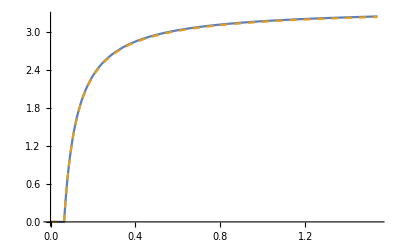

```mathematica
ANA[r_]:=ϕ[r*m2invMeV,RE,λ,A2,β,ρE]
CompAna=Plot[{SOLUTION[z]*10^-6,ANA[z]*10^-6},{z,0,0.04*cutoff},PlotRange->Full,FrameLabel->{Style["x-axis",Bold,12],Style["y-axis",Bold,12]},LabelStyle->{FontFamily->"Arial",FontSize->13},AxesLabel->{MaTeX["z[m]",Magnification->1.2],MaTeX["\\phi (z)[\\text{meV}]",Magnification->1.2]},PlotStyle->{Thick,Dashed},PlotLegends->Placed[Grid[{{LineLegend[{ColorData[97][1]},{MaTeX["\\text{numerical solution}",Magnification->1.2]}],LineLegend[{ColorData[97][2]},{MaTeX["\\text{analytical solution}",Magnification->1.2]}]}}],Below],Exclusions->None]
```

```mathematica
Export["CompAna.pdf",CompAna]
```

CompAna.pdf

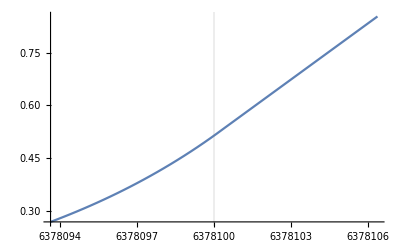

```mathematica
δ=0.000001*R;

Plot[SOLUTION[z],{z,R-δ,R+δ},WorkingPrecision->100,PlotRange->Full,GridLines->{{R}}]
```

## Exclusion plot LLR I

## Compare analytical approximation force vs force from simulation and compute corrected contour

Note that in the following calculations I only compute the relative difference of the (unscreened) force by the simulated dilaton field, compared to the

### Definitions

```mathematica
ϕ[r_,R_,λ_,A2_,β_,ρs_]:=If[r<=R,SetPrecision[ϕρ[A2,λ,β,ρs]+(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρs])/Cosh[μ[A2,λ,β,ρs]R] (1+μ[A2,λ,β,ρV]R)/(μ[A2,λ,β,ρs]+μ[A2,λ,β,ρV]Tanh[μ[A2,λ,β,ρs]R]) Sinh[μ[A2,λ,β,ρs]r]/r,5 CPrec],SetPrecision[ϕρ[A2,λ,β,ρV]-Q[R,ρs,A2,λ,β] (μ[A2,λ,β,ρs]^2 R^3)/3 (ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρs]) E^(-μ[A2,λ,β,ρV](r-R))/r,5CPrec]]

δemN[λ_,A2_,β_,SOLUTION_]:=A2*Abs[Q[A2,λ,β,ρE,ρV,RE]-Q[A2,λ,β,ρM,ρV,RM]]*(SOLUTION[RES/m2invMeV]*SOLUTION'[RES/m2invMeV])/(mpl^2*m2invMeV*aG)
(*This is the analytical expression for the violation of the equivalence principle derived from the approximate solution*)
δem[A2_,λ_,β_]:=If[(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)>=0.1,0,Abs[-1/(9 aG mpl^2 RES^3)A2 ⅇ^((-RES+RS) μ[A2,λ,β,ρV]) RS^3 (Q[A2,λ,β,ρE,ρV,RE]-Q[A2,λ,β,ρM,ρV,RM]) Q[A2,λ,β,ρS,ρV,RS] μ[A2,λ,β,ρS]^2 (1+RES μ[A2,λ,β,ρV]) (ϕρ[A2,λ,β,ρS]-ϕρ[A2,λ,β,ρV]) (ⅇ^((-RES+RS) μ[A2,λ,β,ρV]) RS^3 Q[A2,λ,β,ρS,ρV,RS] μ[A2,λ,β,ρS]^2 (ϕρ[A2,λ,β,ρS]-ϕρ[A2,λ,β,ρV])+3 RES ϕρ[A2,λ,β,ρV])]]
```

```mathematica
(*Note that one was computet in MeV^-1 for distance, one in meter, hence the conversion*)
```

### β = 1, large λ field of sun

```mathematica
(*Note that no comparison for the small lambda region is necessary, since the differential equation is linear in this case and the analytical solution exakt!*)
```

#### A2 = 10^20

```mathematica
(*minMeshSize=SetPrecision[cutoff*10^-11,5 CPrec];*)
```

{47.7656,Null}

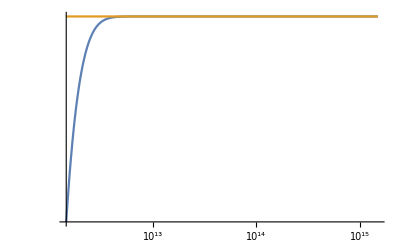

0.36263425860568965187097314980938813465973697537423089305738365180562125267

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^20;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^16

{49.1875,Null}

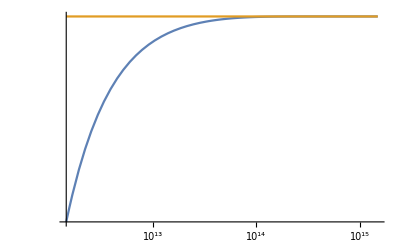

0.54933638974496808872684559211066350116007595127391656763364685025191621738

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^16;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^12

{48.9375,Null}

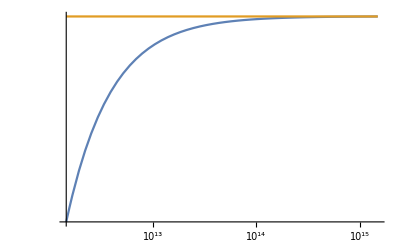

0.727329434085797899880981846030084246986839540307228184974321228514335116

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^12;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^10

{55.4375,Null}

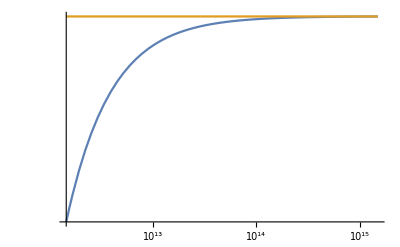

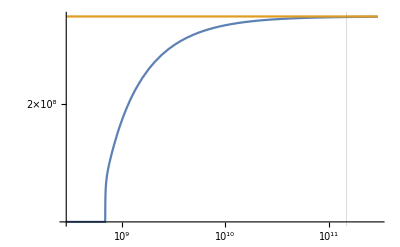

0.8146199505217937952740623399956792418999388684252386672747706092470716547

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^10;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^8

{7.3125,Null}

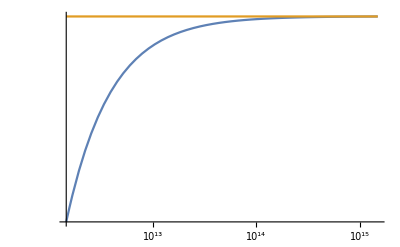

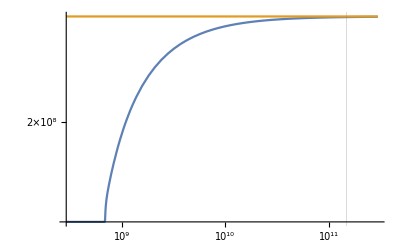

0.89797270546059651437549226204268702591814594325015240587898638959321668227

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^8;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^6

{66.375,Null}

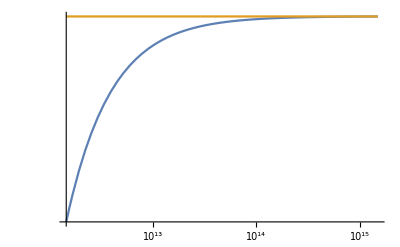

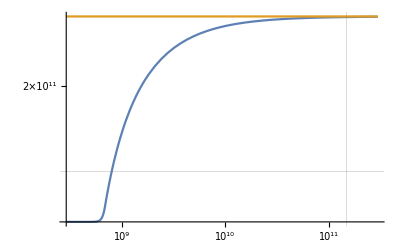

0.93607534522141134039436058351942846379035020757924546095932768515224448969

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(12),1000];
A2=10^6;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^5

{62.3906,Null}

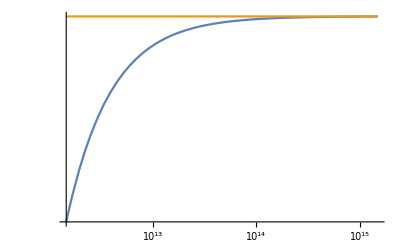

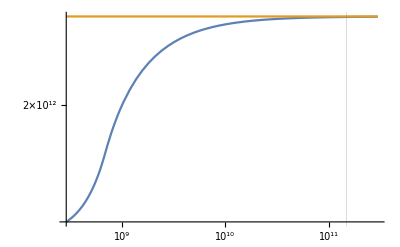

0.59745799451576851258911183747070870570815229621751241112354311053327179983

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(11),1000];
A2=10^5;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^4

{4.1875,Null}

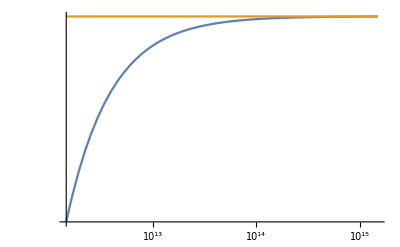

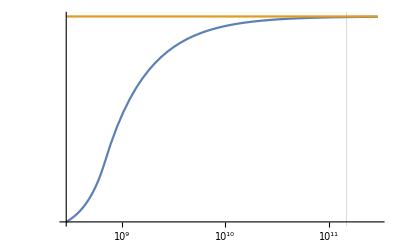

0.12362578647153343945172216752957514222334728991351009120755687464377498314

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(11),1000];
A2=10^4;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^0

{4.32813,Null}

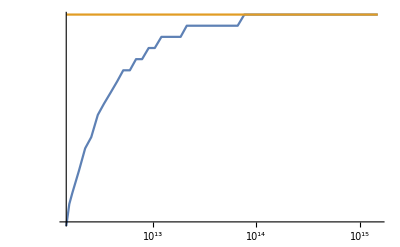

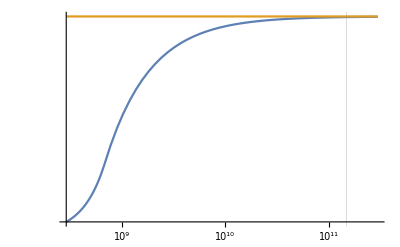

0.041946179823673877073661631866376892606990935166682223122922315620694051879

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(6),1000];
A2=10^0;
β=10^0;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

### Contour correction

As seen above, the analytical approximation and the result from simulations match very well for A2 >= 10^5, for smaller A2 I will compute the correct points along the real contour here.

#### A2 = 10^4, implies λ < 10^10.9

8.48054605870996264568529724599083723540939369295251630933442148749875934934929139051337034745638692946068681841683111094681605752068442358209017768311989464188922017572593599238459304886373645457565380780420656891627480989214993582004313434378617516532574374913335412439913164333047471029387540282730439409896981297014411937586379926306472833722757365532647344186353108907078217818035800610795029908433161390653125114334100697285050205131040849979670399445547649732809644678715009667749733092676684672105503679444223896008350574629247673089469412721774564203465271510136646993391843877714343167290348278503095491351771844194960181993007386063490873263751262298690341142155986535341926545849717416015733919329177819097399697655362736581008618012560754534741886849463092930278542727737755256550158470169142618848756627290325909562358457897838880213989838877059257251406965305702497359674071166386799966909165654798168256071827846776479866114092347815073653959252432833459762003123250155525573331072639×10^-15

{2.75,Null}

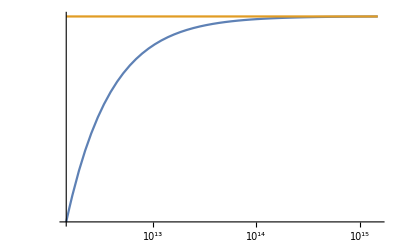

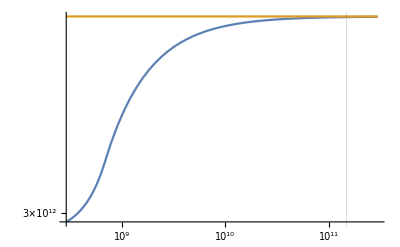

1.24187937929047540605727694645381644408219439631380169904823411909447756906

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(10.9),1000];
A2=10^4;
β=10^0;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

#### A2 = 10^3, implies λ < 10^9.4

7.7493713283391184690463939949912214243548433702697744193209406322540011756324311584364305066566924045623814205072365349267769155600767437890845654710715288126592670046695257921466605140131589983012018800669031068377658148110200344897938171201379873661764371990963716725066086709222827249683068315783580085416007103802391002728000485898966164493649206735560876092030336765900909299212778433997051681981509497993246126671475512769692355667682323715003352422243410520191405325820435317045764540894648412841243015348634549890696661701093648745414843656052121425264162158453724821326854750485051260819849162916718582185431818379682275743844074757420732441690848645336272057088747213724501975337798042498702890368002515474697032847038101575653092640789175664560530674783134748329451017500021743664238303788088679581136704770931291283564576838288104414965352564206395156598568318996311242790393546167184154316673327124202233772140931082507422931687761102322597941836475565445255709505589935704431105236542×10^-13

{2.34375,Null}

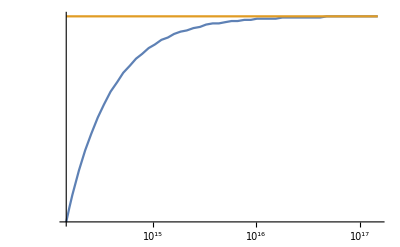

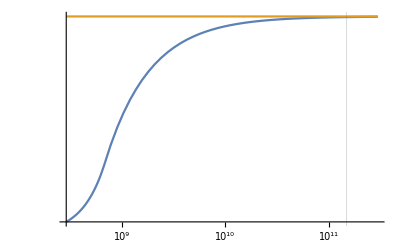

1.08961952300481509637531085693059345939108735951189098167373111903866829448

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(9.4),1000];
A2=10^3;
β=10^0;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

#### A2 = 10^2, implies λ < 10^7.8

1.10681134355801959860880547939088402468447919269600304094980430630519542932101135831391476282962821019101244868585320626851148774073035263925423369760535854232860121946261940467042933920231724735427852296473725530091528173571972293914460232606498895360091001538807415063809139887157623522897481141567200959620355837750634853001123038245453255375405314829743126834251322162875185936808095349641802215031968386880278500431737125913484381634340582916675085794955161395507171237382284227423526598238810702527279857811556862197564623688630318502529751652301290232267664897428254136349374875799024450558491079374320560271122716399344020505894124629141759784084189570768040648096709512253397379693587775017474601997884927268695536623641005653299644962689824222464304131785837105583387864646307486455510392586361785333797641268135503473578975345139449156329765693997953732543702434646637577039076728712433690045543947578129234619503498822121490118997763563207648851060312677426117821303452360309861836808829×10^-10

{4.42188,Null}

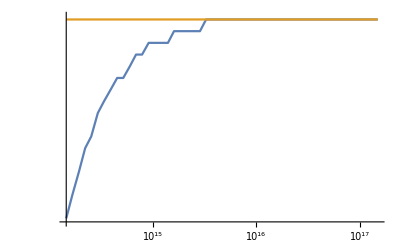

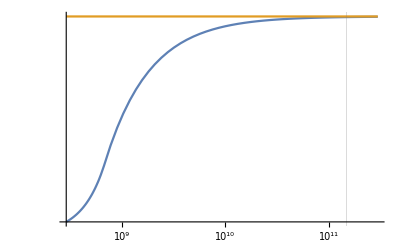

1.39702800261166521144013233988165022274917253887667019274046338783425204022

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(7.8),1000];
A2=10^2;
β=10^0;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

#### A2 = 10^1, implies λ < 10^6.3

1.0019987207723576526307882510601301547429683058692327159960151697859469079503333699600691149648012208590023815825290196899396743414469880546353037807064521920638850392778934918110427463896277866242861310198290389774056802025236933693116624417878320537455261980498041673553964983508769418489098265794815373085191553376094405953391571562570288193192946558094054766120599017142785273097105847953173827975519449782502498322610936632808902456989281669808861811264078972389579621941873305108962681693757030503889240584242547255903987527605477472618701625798298239043036126609160861933388511967693228607302583850277474976917832624232102161844536345065395210130825378451270321954136349181546499613544596124824698313631239062482067282727042234686104728888232546384937359244293572193398706660920140966695274556287874321021184186601155295174718743665622643179171641891214109105453639778635491116891526625613404836126738639902710218830868492954580200164299083350504713335710202340020024217408692459734970827731×10^-8

{3.54688,Null}

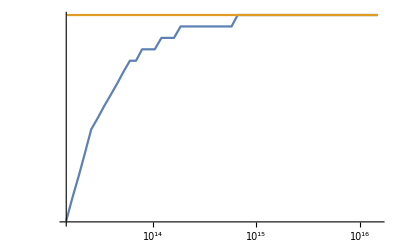

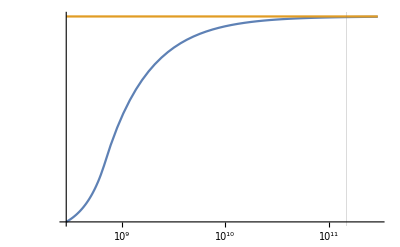

1.1234708848833660239867276696650256767042752979509000540725991326798701987

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(6.3),1000];
A2=10^1;
β=10^0;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

#### A2 = 10^0, implies λ < 10^4.7

1.41497461441355933314623513247974898277235922996604303374421345408111480752673324869917277684727780153788202369092626317609644680173779565629954979060880844896779348566230176267453434517687542718974821729113908102927239142415631568714395428918832108952194743960510773766277767835221247058116352552961439042212628759528959972600450216650730823543587504948167663625214461297069435007197868359528656032345658703870038554832379617206076944158804543655215356903271785990167321670344130719639104499861950299373253772359008668186742683441161156536683018964829230469673663790599604552950394275250634885935347067612812071286921974381661759725372968565889189299356031445198943587487306960011501271702680871406828042175103309461608495749979801609462355745262565637706987644857478616256972776129095055936036268339290762709729566730280889317688539281875820463234748265880135788785443098987218762785780981993499649612811973661000418838754037188995320379817666163374627560595193400492815534621028297715491681244158×10^-6

{3.64063,Null}

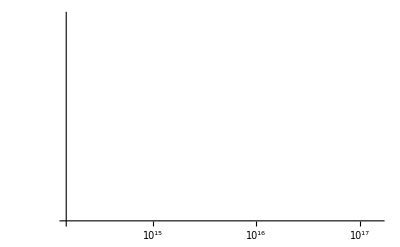

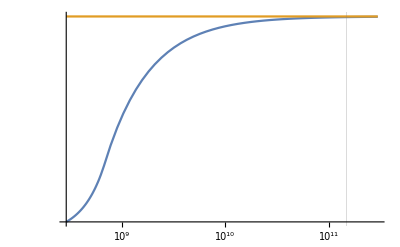

1.38228181694196836031306643274781235386286757813305233711715822843444497605

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(4.7),1000];
A2=10^0;
β=10^0;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

#### A2 = 10^-1, implies λ < 10^3.2

0.000126638345445317909720716095293589045768408246509843145878707908579165500250084261752009954023856156714037994732597720601578342164636990409062465549723452663309942111379441036974594476223063622338895107832472392392090891508044294308885835471073839682357130329608381300797759353734817139171755555228244616346370442777017875786133182027736702911049082629281638579249301447206328782102911724828388523991918522137249341770702691628198845803615688172039129352638950463333972268290196248184641990649988941919173276153036066358676160527044183742855593779856504337243545028929553851306788606646758169005081732567067879562637108638465311355228377515423367812613663883101582527279329971212295318610154898009968820182761551026648400151830030836554452081862152176962584755898108599367038212616009745820545347760148933044990140463580717478328711606168741849982565995299162101593947880430122851759587097692767328089716711887150085233194047623236243191039016302297372790393100614045853002235526829126094363206290964

{3.40625,Null}

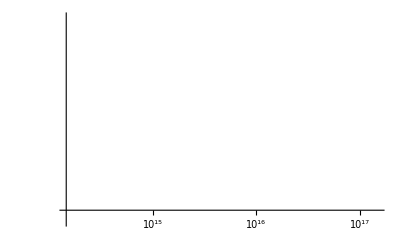

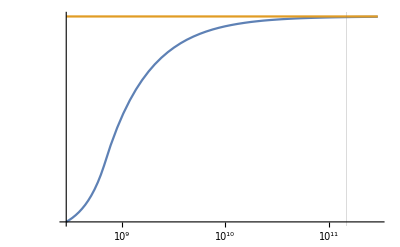

1.06578238412795682602634203430510366357602886322757352605437177995085778785

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(3.2),1000];
A2=SetPrecision[10^-1,1000];
β=10^0;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

#### A2 = 10^-2, implies λ < 10^1.6

0.0176329225024955511156416270420614865610709705863854431346246508805905156508448907392319658071602014075076043967504117273730807576480274606721197149050375846838911980544816413120535647993043416409978602782184903634839173329608860714607517900994231537449400249470160048236699498323183449696826752774758589711197095037564145103604024265275906697964949734803441845374814096009345354978659438952494298572775298967835080552203387732313349185481285184163270314016951137969185466592752260717423627937296597273051580134337809293140299174450678716611802977784541585822100980148966034573335652696881727366728896272969510474741190967605235846841354286033052470900907523464368804789797681461664277114393207973770100333852650062963349462076767700307506255560984682195606234102622913169098226721572104414038145778563478429776741088410382265140058149912166271539049033164895463661005167214604981357891623061008619169903749853398823576303213395695944977950476334514046906581820167543911666831527411007435121824727379

{3.04688,Null}

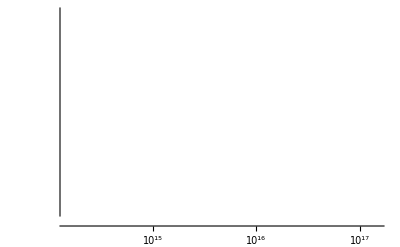

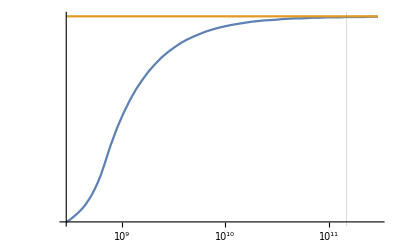

1.22323175553057838505765524261390788201171400507860987371635349051919848297

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(1.6),1000];
A2=SetPrecision[10^-2,1000];
β=10^0;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

### Corrected exclusion β = 1

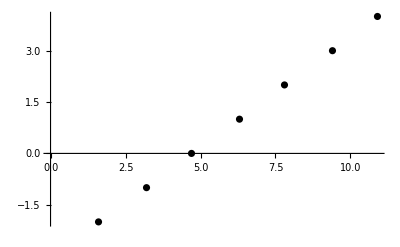

```mathematica
ExclusionLLRIBeta1={{Log10[10^(10.9)],4},{Log10[10^(9.4)],3},{Log10[10^(7.8)],2},{Log10[10^(6.3)],1},{Log10[10^(4.7)],0},{Log10[10^(3.2)],-1},{Log10[10^(1.6)],-2}};
B2=ListPlot[ExclusionLLRIBeta1,PlotStyle->Black]
```

### β = 10^12, large λ field of sun

```mathematica
(*Note that no comparison for the small lambda region is necessary, since the differential equation is linear in this case and the analytical solution exakt!*)
```

#### A2 = 10^4

{54.75,Null}

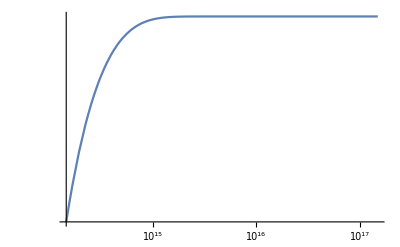

0.61494142910645512894275552773609143529370094896797576372748864589911407181

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^4;
β=10^12;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]-ϕρ[A2,λ,β,ρS]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^0

{54.4531,Null}

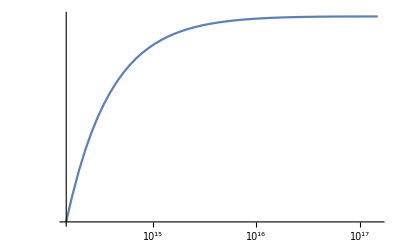

0.79194556156191202114064869501347528077420094790183879303580009082807957449

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^0;
β=10^12;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]-ϕρ[A2,λ,β,ρS]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^-4

{4.95313,Null}

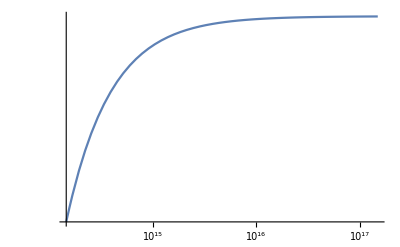

0.94388461885964053225415674079473036922074678539830839325148059888141023815

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=SetPrecision[10^-4,1000];
β=10^12;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]-ϕρ[A2,λ,β,ρS]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

#### A2 = 10^-5

{5.39063,Null}

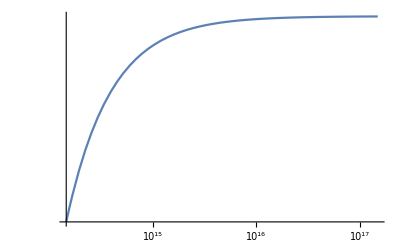

0.90145733285357541326582009394413417652674481398850344196355809415681459829

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=SetPrecision[10^-5,1000];
β=10^12;

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]-ϕρ[A2,λ,β,ρS]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]

δemN[λ,A2,β,SOLUTION]/δem[A2,λ,β]
```

### Contour correction

For A2 > 10^-5 we have seen that the analytical and numerical effect match very well.

#### A2 = 10^-6, implies λ < 10^11.6

0.0000167263577639647466584277431383373988771467274912385789449319374694228631045433941593793343004849465132665876954910330226654358242256549738242341478555133268357901172383879208129302994952928999374676725755163031324862685526962195002735002257002043375492173444344156795094448057674709833923661473743097766756126990598620357451994675799377651271097025172364535875653330247650635883075675486627864842754309518360441993621719781577086865234131533254320080978418355691685506260930755804334718516499239217927681089455149008726035115977944727701999589053506099037172629292649996116972894522651369558626406497065089071096918589016480430993680543323262663364324202808734861675956455552458830695459957224658499956725498278458373310771718157475706298317658322215544577050442983438945858181964923864233667174442629709832898002898173279464072622465515165430913141504128724184229286161120111941038050113583777428315949005440338657170828653820793108255952691507305995849446257252906235002294747002500131439867135032

{3.82813,Null}

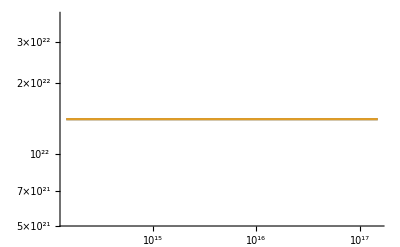

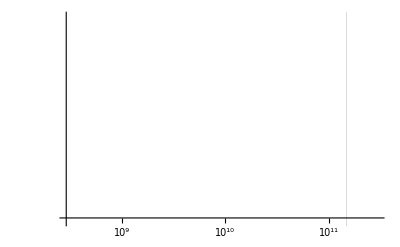

1.16605399642182367227751303304955453093734806555354513067130932548351059075

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(11.6),1000];
A2=SetPrecision[10^-6,1000];
β=10^12;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

#### A2 = 10^-7, implies λ < 10^10.1

0.00167263577638978430947405668485638231888164547904002949655082214823899151520433000956972578534168356638130181535695171756692388198073894336577849024378742028259907927847573239103588985405453408654348139595486978933822204930048883829630254235752097332262390739925994102013696046462489876008331713699715916620034923496825211585942607092212845040148517982930772212756799423869537709889086252352718510597378842288737111290800280372530324792495418642434990569308052658269341905546624731065849816167683480810624421421340441136969779701397969547887232973213193640618509080432978858820218294901360167733290055017082792401812147896302479941368960374060696877409294473379858085986656542233897160002248781219532833649728132501614818434085797166503435588893407864829534256192830953344158189785751835598223299671856354815253768771539894391227575981838152274411371146329874871630197710129489005717910782905547721194573177664173404327606231924602534825204397872225971380793449256288858170394571306285648178670615986

{3.29688,Null}

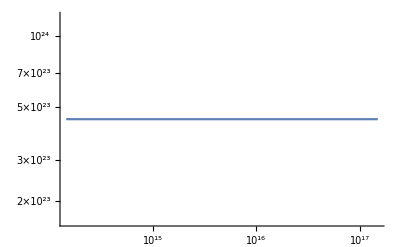

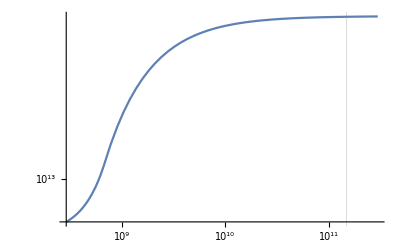

1.17031782191569999448507762876509287448860228339235506225013818287478994536

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(10.1),1000];
A2=SetPrecision[10^-7,1000];
β=10^12;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z]-ϕρ[A2,λ,β,ρS]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

#### A2 = 10^-8, implies λ < 10^8.6

0.16726357763830940083635916223030788397973433653579077100162838070429090832553708110849178215941863874651111492843446898162416816402632777317978330011532147701163984396577184411789117252163849724495495460618810957410582466480453765183695168704802698382925434288234974496696149322746371697920454221544297210419881329993380384987218178269863944931093595005504900245813595546025210784857475778696448103063804755391165703320130195757833549283426332595243988428686577412891157567104051400202947194632315059092433815871592270966533737016530067090759596616688545151377133415313365698626442991496607254523035552801359853240683510041612559649143264334614070421584944855708810827416286405898781580082857653713259487848044679535913716024965708593081728747292318069790259307043778610579360546379623510797108527513186075965560056162095882448900198321301112762536539412365420401746869929067528496264896542149459824630088370518305920509129358620066614152328244279491362609037131881114984429296264325801041121185023

{2.79688,Null}

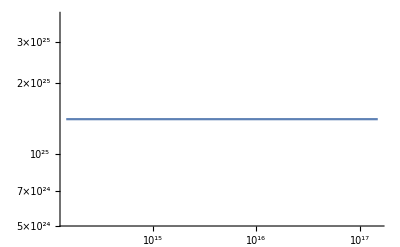

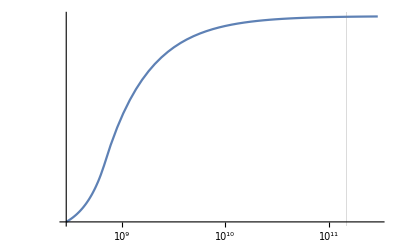

1.17074585114154594306619038111973349834823173898365330682598316311967810637

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(8.6),1000];
A2=SetPrecision[10^-8,1000];
β=10^12;

A2*ϕρ[A2,λ,β,ρV]^2/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

LogLogPlot[{SOLUTION[z]-ϕρ[A2,λ,β,ρS]},{z,0,2*RES/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RES/m2invMeV}}]

δemN[λ,A2,β,SOLUTION]*10^13/2 (*If greater 1 excluded, if smaller 1 not exluded*)
```

### Corrected exclusion β = 10^12

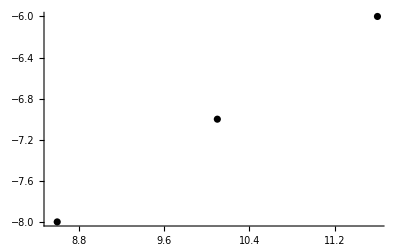

```mathematica
ExclusionLLRIBeta12={{Log10[10^(11.6)],-6},{Log10[10^(10.1)],-7},{Log10[10^(8.6)],-8}};
B3=ListPlot[ExclusionLLRIBeta12,PlotStyle->Black]
```

## Exclusion plot LLR II

Here I only check β = 1, since for larger better LLR I is far better!

### Definitions

```mathematica
(*General Dilaton definitions*)
Clear[ϕρ,Veff,DVeff,DDVeff]
ϕρ[A_,λ_,β_,ρ_]:=SetPrecision[mpl/λ If[2*Log10[λ]+β-Log10[A]-Log10[ρ]<1000000,ProductLog[(λ^2 10^β)/(A ρ)],Log[λ^2/(A ρ)]+1/(6 (β Log[10]+Log[λ^2/(A ρ)])^3) (6 β Log[10] (β Log[10]+Log[λ^2/(A ρ)])^3-6 (-1+β Log[10]+Log[λ^2/(A ρ)]) (1+β^2 Log[10]^2+2 β Log[10] Log[λ^2/(A ρ)]+Log[λ^2/(A ρ)]^2) Log[β Log[10]+Log[λ^2/(A ρ)]]+3 (-3+β Log[10]+Log[λ^2/(A ρ)]) Log[β Log[10]+Log[λ^2/(A ρ)]]^2+2 Log[β Log[10]+Log[λ^2/(A ρ)]]^3)],1000]

μ[A_,λ_,β_,ρ_] :=SetPrecision[ Sqrt[SetPrecision[λ^2  E^SetPrecision[-λ ϕρ[A,λ,β,ρ]/mpl+β/Log10[E],1000] + A ρ,1000]]/mpl,1000]

Veff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/(2 mpl^2) ϕ^2,1000]

DVeff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[-λ/mpl*ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/mpl^2 ϕ,1000]
DDVeff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[λ^2/mpl^2*ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/mpl^2 ,1000]

Q[A_,λ_,β_,ρ_,ρV_,R_]:=If[μ[A,λ,β,ρ] R<100,3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R) Tanh[SetPrecision[μ[A,λ,β,ρ] R,1000]])/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ] Tanh[μ[A,λ,β,ρ] R]),3/(μ[A,λ,β,ρ]^2 R^2)(1 - 1/(μ[A,λ,β,ρ] R))/(1 + μ[A,λ,β,ρV]/μ[A,λ,β,ρ])]

ϕ[r_,R_,λ_,A2_,β_,ρs_]:=If[r<=R,SetPrecision[ϕρ[A2,λ,β,ρs]+(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρs])/Cosh[μ[A2,λ,β,ρs]R] (1+μ[A2,λ,β,ρV]R)/(μ[A2,λ,β,ρs]+μ[A2,λ,β,ρV]Tanh[μ[A2,λ,β,ρs]R]) Sinh[μ[A2,λ,β,ρs]r]/r,5 CPrec],SetPrecision[ϕρ[A2,λ,β,ρV]-Q[R,ρs,A2,λ,β] (μ[A2,λ,β,ρs]^2 R^3)/3 (ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρs]) E^(-μ[A2,λ,β,ρV](r-R))/r,5CPrec]]

δΩdΩ[A2_,λ_, β_]:=If[(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)>=0.1,0,Abs[-1/(18 GN ME mpl^2 REM)A2 ⅇ^((RE-REM) μ[A2,λ,β,ρV]) RE^3 Q[A2,λ,β,ρE,ρV,RE] Q[A2,λ,β,ρM,ρV,RM] μ[A2,λ,β,ρE]^2 (ϕρ[A2,λ,β,ρE]-ϕρ[A2,λ,β,ρV]) (ⅇ^((RE-REM) μ[A2,λ,β,ρV]) RE^3 Q[A2,λ,β,ρE,ρV,RE] μ[A2,λ,β,ρE]^2 (1+2 REM μ[A2,λ,β,ρV] (1+REM μ[A2,λ,β,ρV])) (ϕρ[A2,λ,β,ρE]-ϕρ[A2,λ,β,ρV])+3 REM^3 μ[A2,λ,β,ρV]^2 ϕρ[A2,λ,β,ρV])]]

(*δ is used to approximate the acceleration derivative by a finite difference scheme. in MeV^-1!!*)

δf[SOLUTION_,REM_,A2_]:=A2*Q[A2,λ,β,ρM,ρV,RM]*(SOLUTION[REM/m2invMeV]*SOLUTION'[REM/m2invMeV])/(mpl^2*m2invMeV)
δΩdΩN[A2_,λ_, β_,SOLUTION_, δ_]:=-REM^2/(GN*ME)(δf[SOLUTION,REM,A2]+REM/2*((δf[SOLUTION,(REM+δ),A2]-δf[SOLUTION,(REM-δ),A2])/(2*δ)))
```

### β = 1, large λ comparison analytical vs numerical

#### A2 = 10^24

{59.3281,Null}

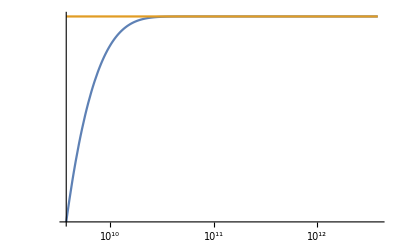

1.7899423374268598513236215321208283989969238886941034199915093705887116712203612485246092111329727767313995035611745808511020125430437412671395119157287756168764936464046428693877311820657847453316754895430700381354595150756691888610716807856751889099183458223534667007426498601937667586052350858532487221752535837788897774934271054688480336230810527938030848605054324935648410212908005979281162052024736496262245565783653132297192760940596477362301579682190640366285841914860238547526782296398026097813871151957936561411022319173687907406625059259086869359267851553893198710691113962121151910219618084643315720762101089445969912110061679325210794435893178589008340754685358177995118469603822994724302490608058963605747239427368514375608307419858346414184333744344236699678624553183680040210131307000664587213753774930068711594929912926787427494419997687250690737092038576019653786310174152433816501789803430111460480986201720374330389541640934430401183035603140599277495965202380716124388

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^24;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]

δΩdΩN[A2,λ, β,SOLUTION, δ]/δΩdΩ[A2,λ, β]
```

#### A2 = 10^20

{59.1406,Null}

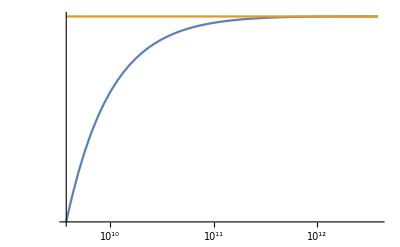

1.8223254265559765026621132614645780611990274181348103282939988953193419078969020729448842733015139536070126784992060792595897302638459737772674649711346829531840652901115456611210713736130656096532200551733970084057802793306071096477936369692199494532817524637391741102685415597924326692816840405438508219332374424274197550574529469893596277869473171195306575014658297447519696649757855651395722696685727085886722460679447407089789334447724078385775860766692354371437326430955764724790720815438778833592666666820545257347901892858635759416628877977537566457501622069786432333988903866635126045978943274800960871714374677399100841069826407141559919624541948593498370514555455087963592022886799853000172244214066972857916637395654074887280541667774434644333875380458278470688241036393069129138475136128742802046023523311707320127295264235811855522190957820380817605397458029143987320101917220050359181655389273723040581598298336886060350526167473786377714582285555273010542945936810050468192

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^20;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]

δΩdΩN[A2,λ, β,SOLUTION, δ]/δΩdΩ[A2,λ, β]
```

#### A2 = 10^16

{59.3594,Null}

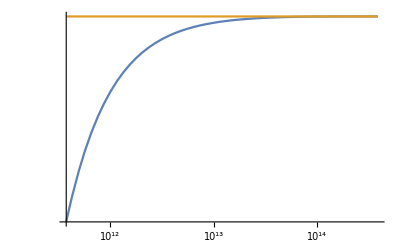

InterpolatingFunction::dmval: Input value {376030.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: (-«708»)/-551553. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: («713»)/(1.04891×10^6) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: («721»)/448486. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {376030.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

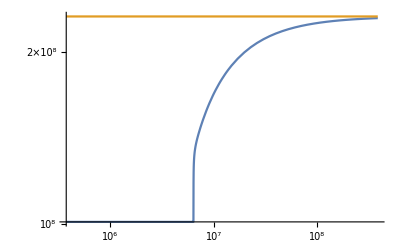

1.9490500664420489484139717070763256775661417925188453947574487501340763133268097793845000860455548106674799480559256223110295896012434094853037278018760713155333899611568173203580312393284740255271184747022589838006417570435413199431821244720365729648287501248693504389860973116021360641991193460804152850807532981929363499317587983187263797833277009339708746404254238791616529582342812451783981649481996279872864664181385095985366651801522311132208435951362415669470239694723112669403747144089635043631717128859943031413697930730657013271540829655375408996785353170168405700881316756115818804918717704944406704152125474795761818896152081595133786339073637468378412444825039150421641458226791195559878730951929545505359607470076333110608480079017225277784022716277634101190757939030857634933653043203011486494954053875301545806785269591260990540599172402072567012213309891071179830073645762291854021609292735519830245724714296240139943594914395532386865150174006830950585845767316758343421

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^16;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full]

δΩdΩN[A2,λ, β,SOLUTION, δ]/δΩdΩ[A2,λ, β]
```

#### A2 = 10^12

{59.1719,Null}

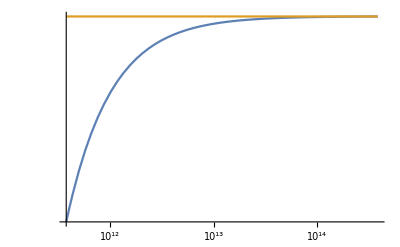

InterpolatingFunction::dmval: Input value {376030.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

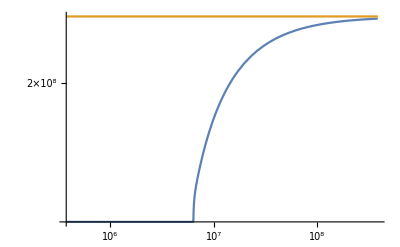

2.54571226307211083637993778917047973291038824068770596508753545940405753327944659809747742006160521287799364338920998014173706188336360292014141862139335316887467682805050388259075671167099771323238396777036079957464439934843878688350247984614504130973167833482165598518378449565035345555415773007712928748375638133396619107910671488663931478509783525655618690425542519881725403308882329749298381343597341100752897880735066282508465254625390513730754057275554853728333703658215605378623325006163370668974424673159833921879996020016090908356094460010743716095969273646942337533219796293896492255331129544647916467873574942914606441029516221500846545771468413092551758336095330661601605862802545593548435910437778354498725108533559180587026414417955903394635939400744564313828537547078580899136202511282107258893396752205706034628335364316850902497874579095293773284030502493050202869326430355192669792063236196601605125533321907161046285131802732068210797327903970367869352053552483764944

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^12;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full]

δΩdΩN[A2,λ, β,SOLUTION, δ]/δΩdΩ[A2,λ, β]
```

#### A2 = 10^8

{4.07813,Null}

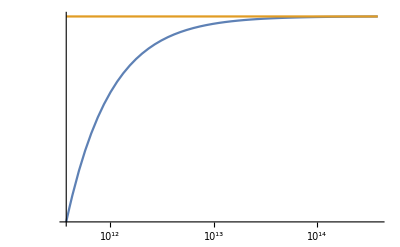

InterpolatingFunction::dmval: Input value {376030.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

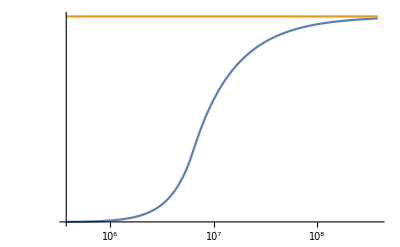

1.451214003021709239267528268607096157233302689822636422137551499327787553664879704770547744403935930536888248930518186903989519859865805171873153086309133149049361942326384728121335407844791228207500165371131202353439587747097571864911134695221315027127028929016343165635010888274969316106320069622696950460370219851736458823520330726354980782921571332112057661347905926469805895577430933876362014553674850773342570630466671099876000751167992913467488399568030920152804330221409380052152369900266843983482838978504456976270632191950586208177493557960225791956218486843700675807674094059190146031160655919578127562812187024580108820976365747681128607169249720886479147466942170907254228294131936958427785370028826659579783206421923116284624119831872268181252285969582368700819317635798113896095126092502301835370735935960215974381434496526616657765262288221401889624766051236306870276800679685103671048991484821

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(15),1000];
A2=10^8;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full]

δΩdΩN[A2,λ, β,SOLUTION, δ]/δΩdΩ[A2,λ, β]
```

#### A2 = 10^6

{5.04688,Null}

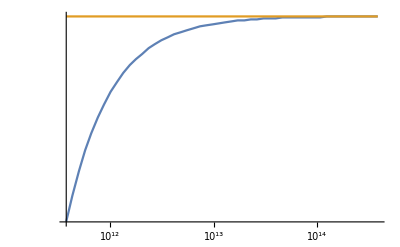

InterpolatingFunction::dmval: Input value {376030.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

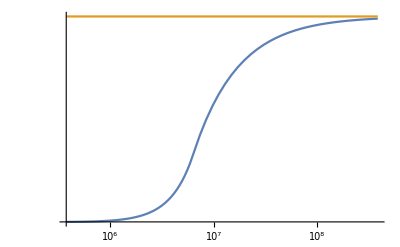

2.249772993510089606407803217536642797590259732021441620985335756533296090045384374079700209154263738581913098935257667476855851324303341825658377475934159359705760694548405772295265834424233734213073218834924953575227138802409336316900684176595547412143193288542957126945556146650384568415564926579810433665432164998135986561644446242570519333020006595478154182851276775779847712173639051512794465178252006377690684619625253062642140930334320550093339582652262687274105115159487210626006401882033316491647252331224767479343676840322994872626209077177247136725926686204511161503892307367428515864974422929533844128840756171205888522770356440337591722631503110433522025078200246551796801699429964101825420459782998820232476261729415388113732644402971960792212569432709483267324670270290059471719415539165340147365905825

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(12),1000];
A2=10^6;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full]

δΩdΩN[A2,λ, β,SOLUTION, δ]/δΩdΩ[A2,λ, β]
```

### Contour correction

The above analysis showed that for A2 >= 10^6 the analytical approximation largely agrees with the numerical solution. For smaller values I will correct the exclusion contour!

#### A2 = 10^5, implies λ < 10^11.8

{4.59375,Null}

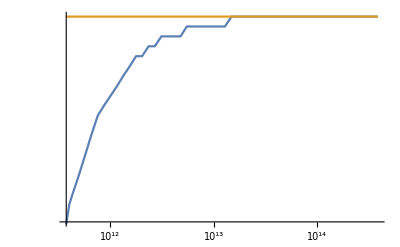

InterpolatingFunction::dmval: Input value {376030.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

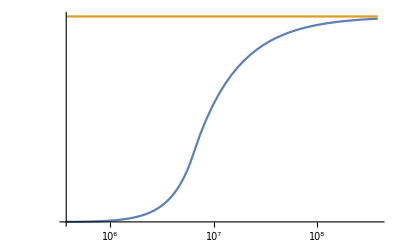

1.37692

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(11.8),1000];
A2=10^5;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12) (*Excluded if greater 1*)
```

#### A2 = 10^4, implies λ < 10^10.9

8.48054605870996264568529724599083723540939369295251630933442148749875934934929139051337034745638692946068681841683111094681605752068442358209017768311989464188922017572593599238459304886373645457565380780420656891627480989214993582004313434378617516532574374913335412439913164333047471029387540282730439409896981297014411937586379926306472833722757365532647344186353108907078217818035800610795029908433161390653125114334100697285050205131040849979670399445547649732809644678715009667749733092676684672105503679444223896008350574629247673089469412721774564203465271510136646993391843877714343167290348278503095491351771844194960181993007386063490873263751262298690341142155986535341926545849717416015733919329177819097399697655362736581008618012560754534741886849463092930278542727737755256550158470169142618848756627290325909562358457897838880213989838877059257251406965305702497359674071166386799966909165654798168256071827846776479866114092347815073653959252432833459762003123250155525573331072639×10^-15

{4.20313,Null}

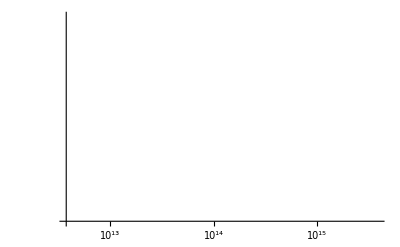

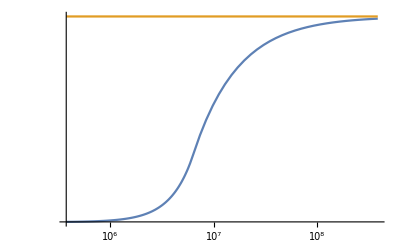

1.05467

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(10.9),1000];
A2=10^4;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12) (*Excluded if greater 1*)
```

#### A2 = 10^3, implies λ < 10^9.8

1.27391301526590593285491813489502603645436324645960671271234484940605432682441973655703081524853865522833949162734257533135415787730239394623433209405291979212320268844183045818138847496106003765447511302752241855087813821604126021784560301720234228836439940641083793431741919602861714042096511151411521553505280812169795715883680235574797388951072779491662765663455856724868940350748098622625493604327306412630279280202978974495811149096575548278856474260798030032807287497266777340557246309773401094502831977589526436605385814982696094378717949936211551423787544637113106284378584383019730865258847973320751015438230262795312963902288353483449080926852606722034039046983137943453771566743054765152271746002910250378019989566021458338796739771655840976424422540896819225142826266031182922269933330344578916781226604465041742852559579821450949365590733020187277893887269464191796811820186571924345815933386267824095415823171467924755220884255640921267036094123225075558761873919940829251179056541899×10^-13

{4.14063,Null}

-Graphics-

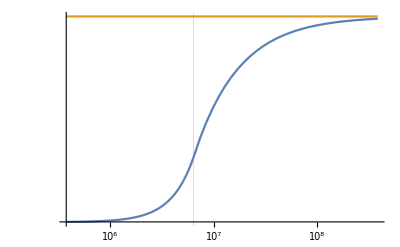

1.49834

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(9.8),1000];
A2=10^3;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12) (*Excluded if greater 1*)
```

#### A2 = 10^2, implies λ < 10^8.8

1.21689431653470579263226200325305934543442749512626252082621263582384374530632557788401944418015499050022700144783913786177538009682939160941207932546026516365433246089918035209182668874624297984116296739976061515519636796726853603849864410415266819832805028642785290602259246985361154607149327230967476492470990197755337454465842047403687378043455315582407657148053162876840343104007688223005294925088218782595618119271738742123948195289873647757815791740126642719323721320267827304914207748269672724771639751318701966372627229124819776154137851707186121101610812508011245777477667340830647741606600348722783508879856363348158905232623912436983015560295982435825991327414453758520558166013437161252586982754881106487123189002447384352133737790091474443772025389319211960413775296940021448644166753396817207546282442112618471014709912899860159549560844149691580145930892501043999120887748510639982932691623790763227734873177934850866808128610860779787811262118286353049119833109053676434435715030441×10^-12

{4.45313,Null}

-Graphics-

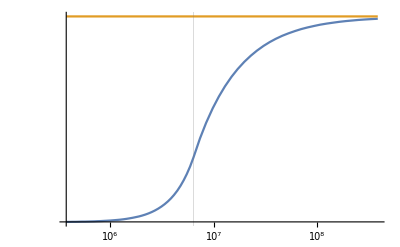

1.43129

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(8.8),1000];
A2=10^2;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12) (*Excluded if greater 1*)
```

#### A2 = 10^1, implies λ < 10^7.8

1.16119386616167570757125246041966912396370472568026538933206025715874702926987209195792637075244626542953774827524753798843696000491990144218887089688208229726696475870158765743154371440939306283963069797568031739435465496777748510758221799958105214322524659817851205212718243171387104933943136254408503821578101225601206669885242274388149875855871398678742704953403954910176685112974647559275221054236390847771187127250491491082322248264805408776995481507041715846230750439618980690670781187883694327605721003901510659793577935082500848116211283941935854257895056724377148085076949066916895423710378697012217553131567896914481272714920719005480516928325405996516690503198097375391851770744048145497220422713511940521420038784065016179621955795393848603296430483595202682166098477912212993396505961418404963847555949443536479359613066345718009216307326606836793594849882445056110231993317941021163690763064451365443302297670516067586243975235277576835356686871925319641595320125374000566188103917917×10^-11

{3.4375,Null}

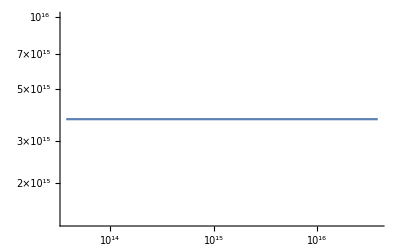

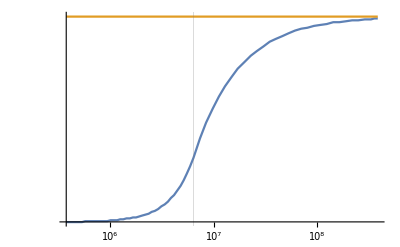

1.36578

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(7.8),1000];
A2=10^1;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12) (*Excluded if greater 1*)
```

#### A2 = 10^0, implies λ < 10^6.8

1.10681134355801934272618390834642613086171844892713294338568267877189538113717606853002391781169022582626247530680627973402017431067126281024684146630255758478163929019181598711341174859797437934035398096686641700711344422845782436153248068518557114316704932919887433935882791476463129291067561766156396643034815255295224992592374123747099354086286991275236226371626653565622977643315919070247904560524550624494378872326266087896660707645276898062952308288437264777636161358887494149421521973476498850021562241682791554560417369302726739717051728376035294815490887478620037432381168882979843696885928124417732500018923116738680468495616264279326538875717943105826208447735161479707695795768993062232834286454286946918226904754696732731911362767401817865453639940603558490262858454911861027256597405470853373104749586700826094036312579135097304134760520400781732631578943771405308833594607933943410803601966546330382897214392397798302318678068985455794883727404660666229442770588015713135525035330981×10^-10

{3.0625,Null}

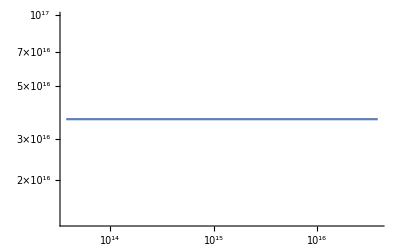

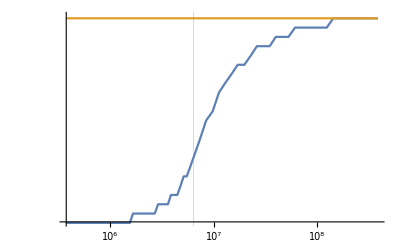

1.30181

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(6.8),1000];
A2=10^0;
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12) (*Excluded if greater 1*)
```

#### A2 = 10^-1, implies λ < 10^5.8

1.053746412657511974252886117667318064028315288197026021782092092088635268837690877561221425131382831×10^-9

{3.03125,Null}

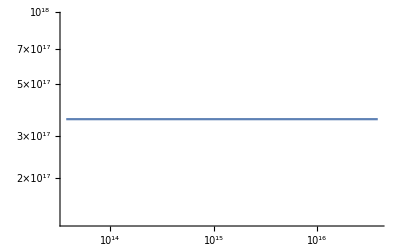

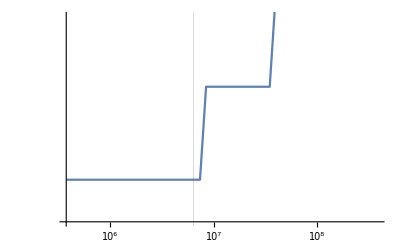

1.2394

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(5.8),1000];
A2=SetPrecision[10^-1,100];
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12) (*Excluded if greater 1*)
```

#### A2 = 10^-2, implies λ < 10^4.8

1.001998720772357747623082841999761583132064941016517143214405048118913077969870285462359703282515947×10^-8

{3.07813,Null}

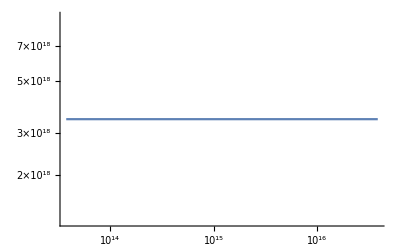

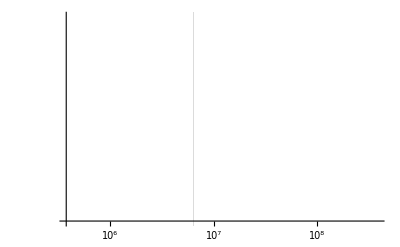

1.17853

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(4.8),1000];
A2=SetPrecision[10^-2,100];
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{SOLUTION[z],ϕρ[A2,λ,β,ρV]},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12) (*Excluded if greater 1*)
```

#### A2 = 10^-4, implies λ < 10^2.8

9.024535525026937997727324419922225516243358465896989348712701873102509830835673175363974788592776881×10^-7

{2.9375,Null}

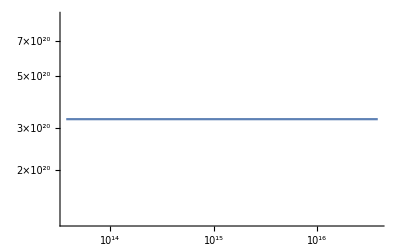

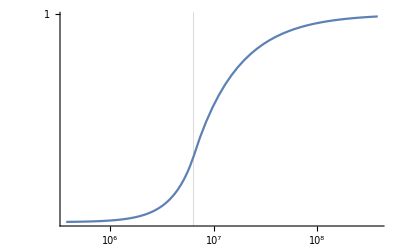

1.06145

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(2.8),1000];
A2=SetPrecision[10^-4,100];
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{(SOLUTION[z]-ϕρ[A2,λ,β,ρE])/(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρE])},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12)
```

#### A2 = 10^-7, implies λ < 10^-0.3

0.001195214639359128816905612950380224106909367584160817042595333530814146990013136787541154888353848763

{2.28125,Null}

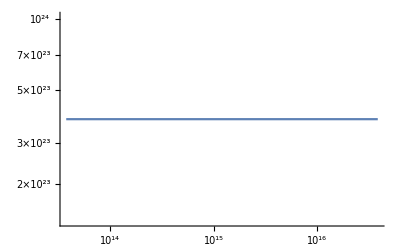

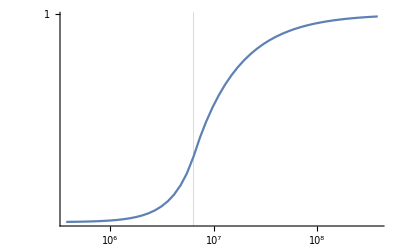

1.40579

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(-0.3),1000];
A2=SetPrecision[10^-7,100];
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{(SOLUTION[z]-ϕρ[A2,λ,β,ρE])/(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρE])},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12)
```

#### A2 = 10^-9, implies λ < 10^-2.3

0.1059126654804196309918852686139326468073092575651120745595350565165451256264080133295296086186621821

{2.35938,Null}

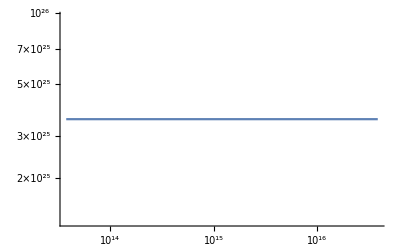

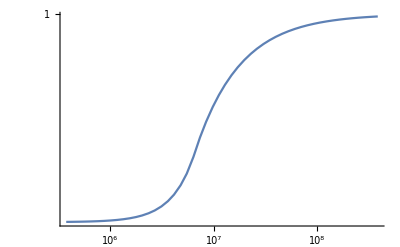

1.24573

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(-2.3),1000];
A2=SetPrecision[10^-9,100];
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeff,DDVeff];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{(SOLUTION[z]-ϕρ[A2,λ,β,ρE])/(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρE])},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/(6.23833*10^-12)
```

```mathematica
ExclusionF={{Log10[7.9*10^30],36},{Log10[1.6*10^31],37},{Log10[2*10^31],38},{Log10[2.1*10^31],39},{Log10[1.9*10^31],40},{Log10[1.2*10^31],41},{Log10[3.8*10^30],42},{Log10[3.3*10^29],43},{Log10[8*10^28],44},{Log10[2.9*10^28],45},{Log10[1.4*10^28],46},{Log10[6*10^27],47},{Log10[2.1*10^27],48},{Log10[6.9*10^26],49}};
B=ListPlot[ExclusionF,PlotStyle->Black];
```

### corrected Exclusion contour β = 1

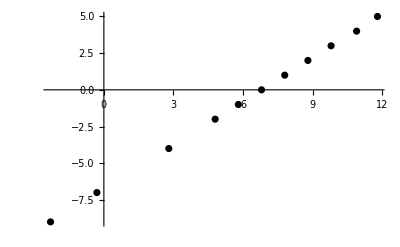

```mathematica
ExclusionLLRII={{Log10[10^(11.8)],5},{Log10[10^(10.9)],4},{Log10[10^(9.8)],3},{Log10[10^(8.8)],2},{Log10[10^(7.8)],1},{Log10[10^(6.8)],0},{Log10[10^(5.8)],-1},{Log10[10^(4.8)],-2},{Log10[10^(2.8)],-4},{Log10[10^(-0.3)],-7},{Log10[10^(-2.3)],-9}};
B=ListPlot[ExclusionLLRII,PlotStyle->Black]
```

## Export for correcte exclusion contours

```mathematica
ExclusionLLRII={{Log10[10^(11.8)],5},{Log10[10^(10.9)],4},{Log10[10^(9.8)],3},{Log10[10^(8.8)],2},{Log10[10^(7.8)],1},{Log10[10^(6.8)],0},{Log10[10^(5.8)],-1},{Log10[10^(4.8)],-2},{Log10[10^(2.8)],-4},{Log10[10^(-0.3)],-7},{Log10[10^(-2.3)],-9}};
B=ListPlot[ExclusionLLRII,PlotStyle->Black]

ExclusionLLRIBeta1={{Log10[10^(10.9)],4},{Log10[10^(9.4)],3},{Log10[10^(7.8)],2},{Log10[10^(6.3)],1},{Log10[10^(4.7)],0},{Log10[10^(3.2)],-1},{Log10[10^(1.6)],-2}};
B2=ListPlot[ExclusionLLRIBeta1,PlotStyle->Black]

ExclusionLLRIBeta12={{Log10[10^(11.6)],-6},{Log10[10^(10.1)],-7},{Log10[10^(8.6)],-8}};
B3=ListPlot[ExclusionLLRIBeta12,PlotStyle->Black]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
BACKGROUND1=ContourPlot[0,{λ,Log10[10^0],Log10[10^17]},{A,Log10[10^-5],Log10[10^29]},Contours-> {1},ContourShading->None,ContourStyle->Directive[Black,Thick,Dashed],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"}),PlotRange->{{-4.8,36},{-16.5,57}}]
```

-Graphics-

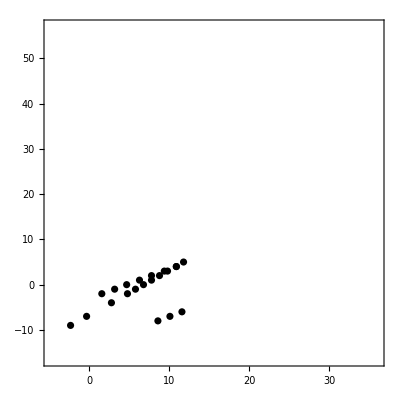

```mathematica
LLR=Show[BACKGROUND1,B,B2,B3]
```

```mathematica
Export["LLR.pdf",LLR]
```

LLR.pdf

## Test

```mathematica
DVeffApprox[ϕ_,A2_,λ_,β_,ρ_] :=  DDVeff[ϕρ[A2,λ,β,ρ],A2,λ,β,ρ]*(ϕ-ϕρ[A2,λ,β,ρ])
DDVeffApprox[ϕ_,A2_,λ_,β_,ρ_] :=   DDVeff[ϕρ[A2,λ,β,ρ],A2,λ,β,ρ]
```

0.0676613805585129964761844857926363669674104483413119449439043768417026782822277512998082843431551605

{1.21875,Null}

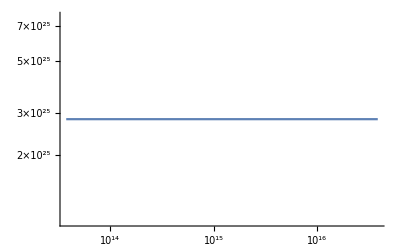

-Graphics-

1.0269946373320492331101680084365679099394270727683106767519402478657557358846641083487926366273×10^17

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(-2.2),1000];
A2=SetPrecision[10^-9,100];
β=10^0;

δ=SetPrecision[0.1*RE,1000];

(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,"Default",DVeffApprox,DDVeffApprox];]

LogLogPlot[{SOLUTION[z]},{z,0,cutoff},WorkingPrecision->100,PlotRange->Full]
LogLogPlot[{(SOLUTION[z]-ϕρ[A2,λ,β,ρE])/(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρE])},{z,0,REM/m2invMeV},WorkingPrecision->100,PlotRange->Full,GridLines->{{RE/m2invMeV}}]

δΩdΩN[A2,λ, β,SOLUTION, δ]/δΩdΩ[A2,λ, β]
```

```mathematica
δΩdΩ[A2,λ, β]
```

0

## Comparison to analytical solution

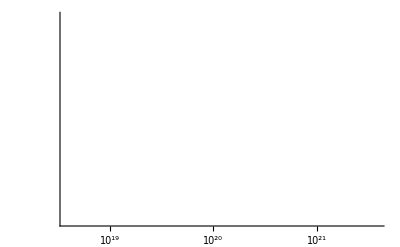

```mathematica
ϕ[r_,R_,λ_,A2_,β_,ρs_]:=If[r<=R,SetPrecision[ϕρ[A2,λ,β,ρs]+(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρs])/Cosh[μ[A2,λ,β,ρs]R] (1+μ[A2,λ,β,ρV]R)/(μ[A2,λ,β,ρs]+μ[A2,λ,β,ρV]Tanh[μ[A2,λ,β,ρs]R]) Sinh[μ[A2,λ,β,ρs]r]/r,5 CPrec],SetPrecision[ϕρ[A2,λ,β,ρV]-Q[A2,λ,β,ρs,ρV,R] (μ[A2,λ,β,ρs]^2 R^3)/3 (ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρs]) E^(-μ[A2,λ,β,ρV](r-R))/r,5CPrec]]

LogLogPlot[{ϕ[r,RE,λ,A2,β,ρE],SOLUTION[r/m2invMeV]},{r,0,2*REM},PlotRange->Full,PlotStyle->{Thick,Dashed},GridLines->{{RS,ϕρ[A2,λ,β,ρV]}}]
```

InterpolatingFunction::dmval: Input value {7865.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

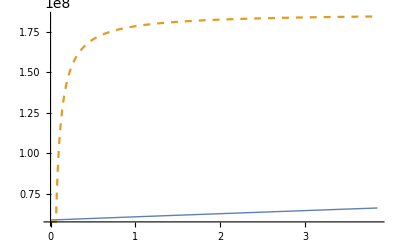

```mathematica
Plot[{ϕI[λ,ρM,A2,β,z*m2invMeV],SOLUTION[z]},{z,0,REM/m2invMeV},PlotRange->Full,PlotStyle->{Thick,Dashed}]
```